# First Set of Projects

Separation of variables for the wave equation with homogeneous Dirichlet conditions in different coordinate systems.

You need: 
1) An analytic solution in terms of special functions.
2) 3D plots of some lower mode shapes.
3) A plot of the lowest few eigenvalues. 
4) Presented as a group poster with suitable references etc.

I will demo later how to confirm your analytical solutions numerically.

### Elliptical Drum Head 2-1 Aspect Ratio

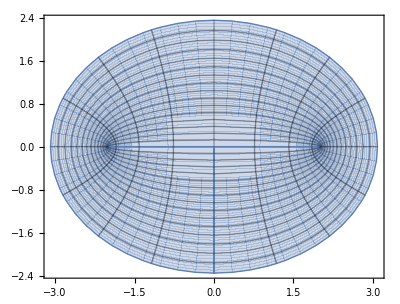

```mathematica
a=2;
ParametricPlot[
{ a Cosh[z] Sin[θ], a Sinh[z] Cos[θ]},
{z, 0,1},{θ,-π,π},
Mesh->True]
```

### Parabolic Drum Head

```mathematica
TabView[{
"2-2"->ParametricPlot[
{ u v, 1/2(v^2-u^2)},
{u, 0,2},{v,-2,2},
Mesh->True],
"4-2"->ParametricPlot[
{ u v, 1/2(v^2-u^2)},
{u, 0,4},{v,-2,2},
Mesh->True]
}]
```

12